```mathematica
Exit[];
```

```mathematica
n=3;
```

```mathematica
x[i_]:=1/(n-1)*(i-1)
```

```mathematica
Table[x[i],{i,n}]
```

{0,1/2,1}

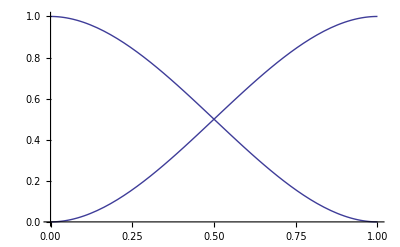

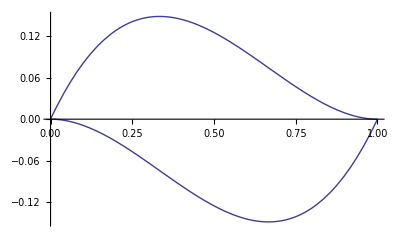

```mathematica
n=2;
x[i_]:=1/(n-1)*(i-1);
M=Join[Table[Table[If[j==0,1,x[i]^j],{j,0,n+1}],{i,n}],Table[Table[If[j==0,0,If[j==1,1,j*i]],{j,0,n+1}],{i,0,1}]];
m=LinearSolve[M];
P=Join[Table[m[Join[Table[KroneckerDelta[k,i],{i,n}],{0,0}]],{k,n}],Table[m[Join[Table[0,{i,n}],Table[KroneckerDelta[k,i],{i,2}]]],{k,2}]];
p[j_]:=Sum[P[[j,k+1]]*x^k,{k,0,n+1}];
Plot[{Table[p[i],{i,n}]},{x,0,1}]
Plot[{Table[p[i+n],{i,1,2}]},{x,0,1},PlotRange->All]
Plot[{Table[D[p[i+n],x]/.x->y,{i,2}]},{y,0,1}];
```

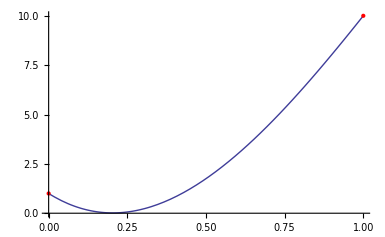

```mathematica
Punkte={1,10,-10,20};Show[Plot[{Sum[Punkte[[k]]*p[k],{k,n+2}]},{x,0,1},PlotRange->All],ListPlot[Table[{x[i],Punkte[[i]]},{i,n}],PlotStyle->Directive[PointSize[Large],Red]]]
```

```mathematica
f[y_]:=ArcTan[100*y];Punkte=Join[Table[f[x[i]],{i,n}],{f'[x[1]],f'[x[n]]}];
```